```mathematica
l:=0.3;
```

```mathematica
alpha := 20.0;
```

```mathematica
vel:=0.1;
```

```mathematica
A:={0.0,0.0};
```

```mathematica
T:={0.0,l};
```

```mathematica
sina:=Sin[alpha*Degree];
```

```mathematica
phi[t_]:=-t*vel*sina/l;
```

```mathematica
XO[t_]:=-l*Cot[alpha*Degree]*Cos[t*vel*sina/l];
```

```mathematica
YO[t_]:=l*Cot[alpha*Degree]*Sin[t*vel*sina/l];
```

```mathematica
XA[t_]:=l*Sin[-phi[t]]+XO[t];
```

```mathematica
YA[t_]:=l*Cos[-phi[t]]+YO[t];
```

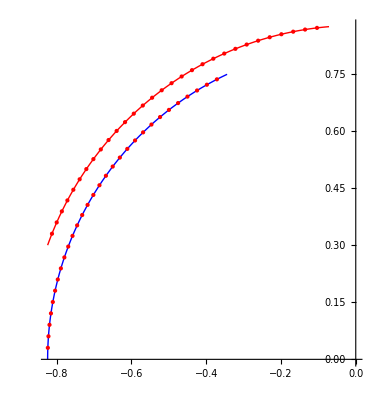

```mathematica
ParametricPlot[{{XA[t],YA[t]},{XO[t],YO[t]}},{t,0,10},Mesh->30,PlotStyle->{Red,Blue}]
```

```mathematica
Odat:=Import["C:/Users/Shmuma/Work/RadioBoat/Sim/Stage1/O.dat"]
Adat:=Import["C:/Users/Shmuma/Work/RadioBoat/Sim/Stage1/A.dat"]
```

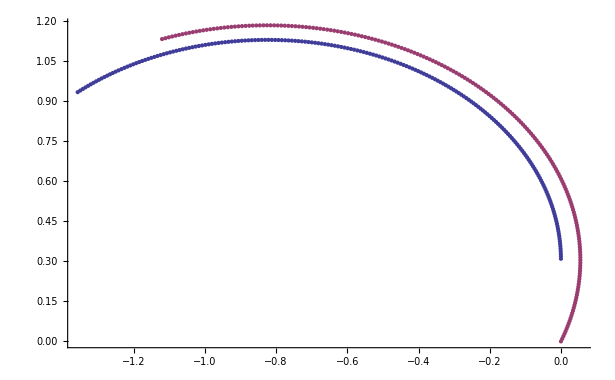

```mathematica
ListPlot[{Odat,Adat}]
```